# Solve for QNMS in the AdS spin - 3/2 fields

## The method

Below is the code that Chen has set up which uses the HH to solve for the QNMs in various dimensions in the case of spin-3/2 fields. 
The method works as follows:
First we determine the value of the potential function, defined as VAdS in this notebook.
Then we can start to apply the method first we need to set U which contains the potential function 
Then S is a function which comes from the HH method as well as T.
M is an expansion function, and contains all the a_i terms which we use to solve for the QNMs
The idea then is that we solve recursively for higher order a_i terms. And we plug these values into the equation that describes our wave equation (S*Y)+(T*Z)+(U*X)
Once we have solved for once we have a solution for all the a_i terms, we plug these solutions in Eq M
Once these  are plugged we have equation of χ and ω choosing our values of χ we can solve for ω.

## What this code does

This code runs through the dimensions of D=5 to D=8. I have chosen these values since we know 4 dimensions does not behave correctly and, from what ive seen from our previous works, the 9 dimensional case could be pushing the method to a limit where we don’t get sensible results.
This code then runs through different recursion depths. Its starts with and iteration of 4 and then goes up to the value set by TK. 
In this case since we have the a terms increasing in half units we end up with double the number of a values as compared to the current iteration depth goal. That is we have 8 terms upto 2TK terms. 
It should be noted that in all cases in this code it is only looking at the l=0 mode of the field

### Understanding the printed out results

While it is running the first number after the loop is the dimension it is currently working on.
Then the results it print are all values of ω where Re[ω]>= 0 and -1<= Im[ω]<=0. I have chosen these limits since we know that negative rela values are unphysical, and values with Im[ω] outside of these boundaries should disappear so quickly that they don’t necessarily constitute as realistic solutions.
I have also printed out lists of results so that we can see if and of the solutions converge as this should suggest which ones are more likely to be stabel solutions as opposed to solutions that exist purely because of the order we are investigating. 
UPDATE:
The code now prints out a plot showing the QNMS. I have added this as it should make it clearer if the QNMs are moving to a specfic value or are just random.

## The Code

```mathematica
TK=14; (*Set the max iteration depth*)
Monitor[Do[Clear[TotΛ,TotM,l,barλ];
PlotNum=0;
Mon=0;
Print["QNMs for the case of D=",TotDim];
     TotM=M;
l=1;
barλ =(l+3/2)+((TotDim-3)/(2));
TotΛ=-(((TotDim-2)(TotDim-1))/2);
     f[r_]:=1-2*TotM/r^(TotDim-3)-((2*TotΛ*r^(2))/((TotDim-2)(TotDim-1)));
(*prerequistis for setting up the potential*)BB[r_,ω_]=(I*barλ* ((f[r])^(1/2))/r)*(1+((TotDim-2)*(TotDim-3)*TotM/((-barλ^(2)+((TotDim-2)^(2)/(4))f[r]+(((TotDim-2)*r^(2)*TotΛ)/(2(TotDim-1))))*r^(TotDim-3))));
DD[r_,ω_]= ((-I*r*(TotΛ*(TotDim-2)/(2*(TotDim-1)))^(1/2)*(f[r])^(1/2))/r)*(((TotDim-4)/(TotDim-2))+((TotDim-2)*(TotDim-3)*TotM/((-barλ^(2)+((TotDim-2)^(2)/(4))f[r]+(((TotDim-2)*r^(2)*TotΛ)/(2(TotDim-1))))*r^(TotDim-3))));
FF[r_,ω_]=(1+(f[r]/(2*ω))*(D[(DD[r,ω]/(ⅈ*BB[r,ω])),r])*((BB[r,ω])^2/((BB[r,ω])^2-(DD[r,ω])^2)))^-1;
W[r,ω]=((DD[r,ω])^2-(BB[r,ω])^2)^(1/2)*FF[r,ω];
AdSV[r_,ω_]=(W[r,ω])^2+(f[r]*FF[r,ω]*D[W[r,ω],r]);
(*The potential function is now setup*)
Do[Print["We have used ", k, " iterations"];
(* This loop goes through all the iterations starting at some value and then ending at TK*)
Mon=0;
(*Here we setup the HH method*)
Simplify[Simplify[AdSV[r,ω]/(f[r]*FF[r,ω])/.r->(1/x)]/.M->(1/2)*(((χ^(2)+1)/(χ^(TotDim-1))))];
U=Series[Simplify[(x-χ)*Simplify[(AdSV[r,ω]/(f[r]*FF[r,ω]))/.r->(1/x)]/.M->(1/2)*(((χ^(2)+1)/(χ^(TotDim-1))))],{x,χ,k}];
S=Series[Simplify[Simplify[Simplify[((x^4)*(f[r]*FF[r,ω])/(x-χ))/.r->(1/x)]/.M->(1/2)*(((χ^(2)+1)/(χ^(TotDim-1))))]],{x,χ,k}];
T=Series[Simplify[Simplify[(2*x^3*(f[r]*FF[r,ω]))-((D[(f[r]*FF[r,ω]),r]-2*I*ω)*(x^2))/.r->(1/x)]/.M->(1/2)*(((χ^(2)+1)/(χ^(TotDim-1))))],{x,χ,k}];
M[x_,χ_]:=Sum[Subscript[a, i/2]*(x-χ)^(i/2),{i,0,2k}];
(*All appropriate functions for the HH method are defined*)
X=(M[x,χ]/((x-χ)^2));
Z=Simplify[(D[M[x,χ],x]/(x-χ))];
Y=Simplify[D[M[x,χ],{x,2}]];
Collect[(S*Y)+(T*Z)-(U*X),(x-χ)] ;
Equation = (S*Y)+(T*Z)-(U*X); (*These two variables are used a temporary holding functions which can be updated in the calculation*)
Equation2 = M[x,χ];
Do[Temp = Subscript[a, (i/2)]/. First[Simplify[Solve[Coefficient[Equation,(x-χ),(i-4)/2]==0,  Subscript[a, (i/2)]]]]; (*This loop finds solutions for the Subscript[a, i/2] terms and pluggs them into the equation of S*Y + T*Z-U*X*)
Equation = Equation /.  Subscript[a, (i/2)]-> Temp;
Equation2 =Equation2/. Subscript[a, (i/2)]-> Temp;
Mon=i;
Clear[Temp];,{i,1,2k}]; 
 Equation3 =(Equation2/Subscript[a, 0])/.{x-> 0,χ->1};(*Then plug the values of Subscript[a, i/2] into the function M*)
Sol=NSolve[Equation3==0&&Re[ω]≥0&&Im[ω]≤0,ω];(* THen we solve for the values of ω (At the moment I have limits on the value of ω where this comes purely from intuition)*)
(*This ends the solving part of the code the next bit is used to plot the graphs*)
Dimi=Dimensions[Sol][[1]];(* We need to check if there actually exist solutions*)
If[Dimi>0, (*If there are solutions  then we can plot a graph*)
Solutions=ω/.Sol; (* Make the solutions purely numerical*)
SolTable=Table[i,{i,0,Dimensions[Solutions][[1]]-1},{j,0,1}];
Do[SolTable[[i,1]]= Re[Solutions[[i]]];
SolTable[[i,2]]= Im[Solutions[[i]]];,{i,1,Dimensions[Solutions][[1]]}];(*Place these solutions in a table so they can be plotted*)
If[PlotNum==0,
p[PlotNum]=ListPlot[SolTable,PlotStyle->RGBColor[0.5,(1/TK)*k,0],AxesLabel-> {"Re","Im"},PlotLegends->{k" Iteration"}];,
If[k==TK,
p[PlotNum]=ListPlot[SolTable,PlotStyle->RGBColor[0.5,(1/TK)*k,0],AxesLabel-> {"Re","Im"},PlotLegends->{k" Iterations"}];,
p[PlotNum]=ListPlot[SolTable,PlotStyle->RGBColor[0.5,(1/TK)*k,0],AxesLabel-> {"Re","Im"}]]];
PlotNum=PlotNum+1;,Sol=0];
Print[Sol];,{k,4,TK}];
PlotList=Table[p[i],{i,0,PlotNum-1}];(*Gather up all the plots created so that they can be shown by the function Show*)
Print[Show[PlotList,PlotRange-> {{0,10},{-20,0}}]];
Print[Show[PlotList,PlotRange->All]],{TotDim,5,9}];,Mon]
```

QNMs for the case of D=5

We have used 4 iterations

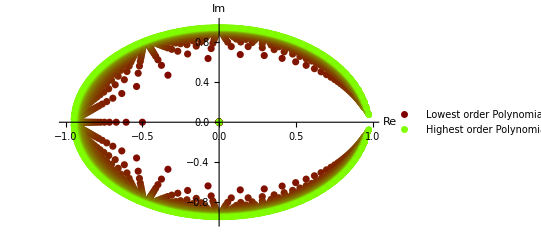

```mathematica
TotRuns=100;
l=0;
ColorTable={{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}};
Monitor[Do[Clear[SolTable];
Sol=Solve[Sum[i^(1)r^(i),{i,0,k}]==0,r];
Dimi=Dimensions[Sol][[1]];
If[Dimi>0,
Solutions=r/.Sol;
SolTable=Table[i,{i,0,Dimensions[Solutions][[1]]-1},{j,0,1}];
Do[SolTable[[i,1]]= Re[Solutions[[i]]];
SolTable[[i,2]]= Im[Solutions[[i]]];,{i,1,Dimensions[Solutions][[1]]}];
ColorList=Table[0,{i,1,Dimensions[Solutions][[1]]}];
If[l==0,
p[l]=ListPlot[SolTable,PlotStyle->RGBColor[0.5,(1/TotRuns)*k,0],AxesLabel-> {"Re","Im"},PlotLegends->{"Lowest order Polynomial"}];,
If[k==TotRuns,
p[l]=ListPlot[SolTable,PlotStyle->RGBColor[0.5,(1/TotRuns)*k,0],AxesLabel-> {"Re","Im"},PlotLegends->{"Highest order Polynomial"}];,
p[l]=ListPlot[SolTable,PlotStyle->RGBColor[0.5,(1/TotRuns)*k,0],AxesLabel-> {"Re","Im"}];];];
l=l+1;,Solutions=0];,{k,0,TotRuns}];,k]
PlotList=Table[p[i],{i,0,l-1}];
Show[PlotList,PlotRange->{{-1,1},{-1,1}}]
```